# Electronic Structure of Graphene using TBA and p_z Atomic Orbitals

Angel Salazar
School of Physical Sciences and Nanotechnology

-Graphics-

Let' s define the vector κ and the lattice parameters;

```mathematica
κ = {kx,ky};
a1 =a/2{√3,1};
a2 =a/2{√3,-1};
```

Let’s simplify the off diagonal term of the associated Hamiltonian:

```mathematica
tπ(1+Exp[-ⅈ κ.a1]+Exp[-ⅈ κ.a2])//ExpToTrig//FullSimplify
```

tπ+2 ⅇ^(-1/2 ⅈ √3 a kx) tπ Cos[(a ky)/2]

Let' s enter  the Hamiltonian elements :

```mathematica
h[1,1]=h[2,2]=ep;
h[1,2]=tπ(1+2 ⅇ^(-1/2 ⅈ √3 a kx) Cos[(a ky)/2]);
h[2,1]=tπ(1+2 ⅇ^(1/2 ⅈ √3 a kx) Cos[(a ky)/2]);
```

```mathematica
H=Table[h[i,j],{i,2},{j,2}];
H//MatrixForm
```

(ep | tπ (1+2 ⅇ^(-1/2 ⅈ √3 a kx) Cos[(a ky)/2])
tπ (1+2 ⅇ^(1/2 ⅈ √3 a kx) Cos[(a ky)/2]) | ep)

```mathematica
eigenv =Eigenvalues[H]//FullSimplify//PowerExpand
```

{ep-tπ √(3+4 Cos[1/2 √3 a kx] Cos[(a ky)/2]+2 Cos[a ky]),ep+tπ √(3+4 Cos[1/2 √3 a kx] Cos[(a ky)/2]+2 Cos[a ky])}

Let’s compute the reciprocal lattice vectors

```mathematica
a1 =a/2{√3,1,0};
a2 =a/2{√3,-1,0};
a3 = {0,0,1};
b1 = ((2π a2×a3)/(a1.(a2×a3)))[[{1,2}]]
```

{(2 π)/(√3 a),(2 π)/a}

```mathematica
b2 = ((2π a3×a1)/(a1.(a2×a3)))[[{1,2}]]
```

{(2 π)/(√3 a),-(2 π)/a}

Let' s  plot the band structure in 3D

```mathematica
Plot3D[Table[eigenv[[i]],{i,2}]/.{ep->0,tπ->1,a->√2 π}//Evaluate,{kx,-2/(√3),2/(√3)},{ky,-2/(√3),2/(√3)},
MaxRecursion->2,
PlotPoints->30,
BoxRatios->{1, 1, 1.3},
AxesLabel->{"kx","ky","Energy (eV)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->15},
AxesOrigin->{0,0,0},
BoundaryStyle->{Blue,AbsoluteThickness[1]},
PlotStyle->Opacity[0.8],
ViewPoint->{0,0,∞}

]
```

-Graphics3D-

Let’s  manipulate this BS  changing ϵ_p and t_π to see if we can open a band gap

```mathematica
Manipulate[Plot3D[Table[eigenv[[i]],{i,2}]/.{ep->epval,tπ->tπval,a->√2 π}//Evaluate,{kx,-2/(√3),2/(√3)},{ky,-2/(√3),2/(√3)},
MaxRecursion->2,
PlotPoints->30,
BoxRatios->{1, 1, 1.3},
AxesLabel->{"kx","ky","Energy (eV)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->15},
AxesOrigin->{0,0,0},
BoundaryStyle->{Blue,AbsoluteThickness[1]},
PlotStyle->Opacity[0.8],
ViewPoint->{0,0,∞}

],{{epval,0,"ϵ_p"},-2,2},{{tπval,1,"tπ"},-2,2},ControlPlacement->Right]
```

From this result, it is not possible to manipulate the band gap with the parameters ϵ_p and t_π

Let' s visualize the band structure within the IBZ

```mathematica
Plot3D[Table[eigenv[[i]],{i,2}]/.{ep->0,tπ->1,a->√2 π}//Evaluate,{kx,0,1/(√3)},{ky,0,1/3},
MaxRecursion->2,
PlotPoints->80,
BoxRatios->{1, 1, 1},
AxesLabel->{"kx","ky","Energy (eV)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->15},
AxesOrigin->{0,0,0},
BoundaryStyle->{Blue,AbsoluteThickness[1]},
PlotStyle->Opacity[0.8],
ViewPoint->{0,0,∞},
RegionFunction->Function[{x,y,z},y<x/(√3)&&x≥0 && y≥0]
]
```

-Graphics3D-

Let' s  compute the BS along the high symmetry points: Γ-M-K-Γ

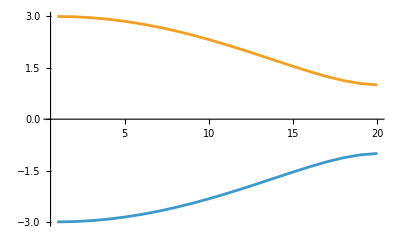

```mathematica
Table[ΓM[i]=Table[eigenv[[i]]/.{ep->0,tπ->1,a->2 π,ky->0},{kx,0,1/(√3),0.03}
],{i,2}];

pathΓM=ListPlot[Table[ΓM[i]//Chop[#,10^-5]&//MapIndexed[{First[#2]+0,#1}&,#]&,{i,2}],
Joined->True,
PlotRange->All
]
```

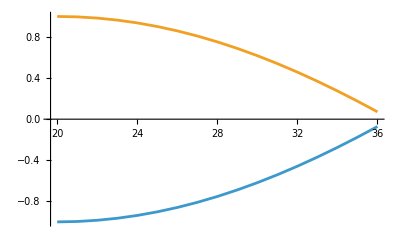

```mathematica
Table[MK[i]=Table[eigenv[[i]]/.{ep->0,tπ->1,a->2 π,kx->1/(√3)},{ky,0,1/3,0.02}


],{i,2}];

pathMK=ListPlot[Table[MK[i]//Chop[#,10^-5]&//MapIndexed[{First[#2]+19,#1}&,#]&,{i,2}],
Joined->True,
PlotRange->All

]
```

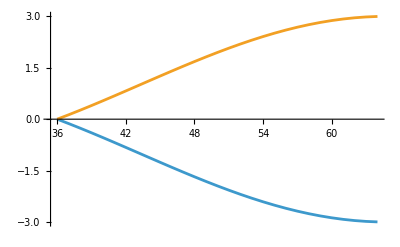

```mathematica
Table[KΓ[i]=Table[eigenv[[i]]/.{ep->0,tπ->1,a->2 π,ky->kx/(√3)},{kx,1/(√3),0,-0.02}


],{i,2}];

pathKΓ=ListPlot[Table[KΓ[i]//Chop[#,10^-5]&//MapIndexed[{First[#2]+35,#1}&,#]&,{i,2}],
Joined->True,
PlotRange->All

]
```

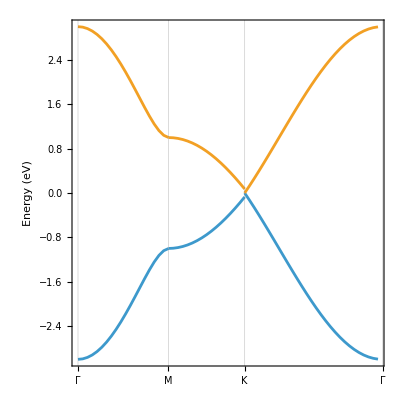

```mathematica
gridline={1,20,36,65};
hsplabel={"Γ","M","K","Γ"};
Show[pathΓM,pathMK,pathKΓ,
PlotRange->All,
Frame->True,
FrameLabel->{"","Energy (eV)"},
Axis->None,
AspectRatio->1,
GridLines->{gridline,None},
FrameTicks->{{Automatic,None},{{gridline,hsplabel}//Transpose,None}},
BaseStyle->{FontFamily->"Helvetica",FontSize->15}
]
```

The dirac point is telling us the directions.

Let’s visualize  the dirac cones

```mathematica
Plot3D[Table[eigenv[[i]],{i,2}]/.{ep->0,tπ->1,a->√2 π}//Evaluate,{kx,-0.15,0.15},{ky,2/3-0.15,2/3+0.15},
MaxRecursion->2,
PlotPoints->30,
BoxRatios->{1, 1, 1.3},
AxesLabel->{"kx","ky","Energy (eV)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->15},
AxesOrigin->{0,0,0},
BoundaryStyle->{Blue,AbsoluteThickness[1]},
PlotStyle->Opacity[0.8],
ViewPoint->{0,0,∞}
]
```

-Graphics3D-